## B - spline

```mathematica
Subscript[P, 0] = {{0},{0}};
Subscript[P, 2] = {{10},{53}};
(*Subscript[P, 1] = {{0.5},{0.5}};*)
Subscript[P, 1]= {Sqrt[(Subscript[P, 0][[1]]-Subscript[P, 2][[1]])^2]/2,Sqrt[(Subscript[P, 0][[2]]-Subscript[P, 2][[2]])^2]/2};
Subscript[Q, 0] = Subscript[P, 2];
Subscript[Q, 2] = {{80},{-32}};
Subscript[R, 0] = Subscript[Q, 2];
Subscript[R, 2] = {{62},{20}};
```

```mathematica
Subscript[P, 0] = {{0},{0}};
Subscript[P, 2] = {{10},{53}};
(*Subscript[P, 1] = {{0.5},{0.5}};*)
Subscript[P, 1]= {Sqrt[(Subscript[P, 0][[1]]-Subscript[P, 2][[1]])^2]/2,Sqrt[(Subscript[P, 0][[2]]-Subscript[P, 2][[2]])^2]/2};
Subscript[Q, 0] = Subscript[P, 2];
Subscript[Q, 2] = {{40},{53}};
Subscript[R, 0] = Subscript[Q, 2];
Subscript[R, 2] = {{62},{53}};
Subscript[M, 0] = Subscript[R, 2];
Subscript[M, 2] = {{80},{53}};
```

### Esempio numerico

```mathematica
Subscript[P, i_] := {{Subscript[a, i]},{Subscript[b, i]}}
```

```mathematica
Subscript[Q, i_] := {{Subscript[c, i]},{Subscript[d, i]}}
```

```mathematica
Subscript[R, i_] := {{Subscript[e, i]},{Subscript[f, i]}}
```

```mathematica
Subscript[M, i_] := {{Subscript[g, i]},{Subscript[h, i]}}
```

```mathematica
Subscript[P, 1]
```

{{5},{53/2}}

```mathematica
Subscript[P, 2]
```

{{10},{53}}

```mathematica
Subscript[R, 1]
```

{{e_1},{f_1}}

```mathematica
Subscript[M, 1]
```

{{g_1},{h_1}}

### Curve 1 e 2

```mathematica
Subscript[B, 1]= Binomial[2,0]*Subscript[P, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[P, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[P, 2]*(1-l)^0*l^2
```

{{10 (1-l) l+10 l^2},{53 (1-l) l+53 l^2}}

```mathematica
Subscript[B, 2]= Binomial[2,0]*Subscript[Q, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[Q, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[Q, 2]*(1-l)^0*l^2
```

{{10 (1-l)^2+40 l^2+2 (1-l) l c_1},{53 (1-l)^2+53 l^2+2 (1-l) l d_1}}

```mathematica
Subscript[dB, 1] = D[Subscript[B, 1],l]
```

{{10 (1-l)+10 l},{53 (1-l)+53 l}}

```mathematica
Subscript[dB, 2] = D[Subscript[B, 2],l]
```

{{-20 (1-l)+80 l+2 (1-l) c_1-2 l c_1},{-106 (1-l)+106 l+2 (1-l) d_1-2 l d_1}}

```mathematica
eq = Flatten[(Subscript[dB, 1]/.l-> 1)] - Flatten[(Subscript[dB, 2]/.l-> 0) ]
```

{30-2 c_1,159-2 d_1}

```mathematica
sol = Solve[eq == 0]
```

{{c_1→15,d_1→159/2}}

```mathematica
Subscript[curva, 1] = Subscript[B, 1]
```

{{10 (1-l) l+10 l^2},{53 (1-l) l+53 l^2}}

```mathematica
Subscript[curva, 2] = Subscript[B, 2]/.sol
```

{{{10 (1-l)^2+30 (1-l) l+40 l^2},{53 (1-l)^2+159 (1-l) l+53 l^2}}}

```mathematica
(Subscript[B, 1]) // MatrixForm
```

(10 (1-l) l+10 l^2
53 (1-l) l+53 l^2)

```mathematica
(Subscript[B, 2]) // MatrixForm
```

(10 (1-l)^2+40 l^2+2 (1-l) l c_1
53 (1-l)^2+53 l^2+2 (1-l) l d_1)

```mathematica
Subscript[Q, 1]/.sol
```

{{{15},{159/2}}}

### Curva 3

```mathematica
Subscript[B, 3]= Binomial[2,0]*Subscript[R, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[R, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[R, 2]*(1-l)^0*l^2
```

{{40 (1-l)^2+62 l^2+2 (1-l) l e_1},{53 (1-l)^2+53 l^2+2 (1-l) l f_1}}

```mathematica
Subscript[dB, 3] = D[Subscript[B, 3],l]
```

{{-80 (1-l)+124 l+2 (1-l) e_1-2 l e_1},{-106 (1-l)+106 l+2 (1-l) f_1-2 l f_1}}

```mathematica
eeq = Flatten[(Subscript[dB, 2]/.l-> 1)] - Flatten[(Subscript[dB, 3]/.l-> 0) ]
sol1 = Solve[eeq == 0]
```

{160-2 c_1-2 e_1,212-2 d_1-2 f_1}

{{e_1→80-c_1,f_1→106-d_1}}

```mathematica
sol1 = sol1/. sol
```

{{{e_1→65,f_1→53/2}}}

```mathematica
Subscript[curva, 3] = Subscript[B, 3]/.sol1
```

{{{{40 (1-l)^2+130 (1-l) l+62 l^2},{53 (1-l)^2+53 (1-l) l+53 l^2}}}}

### Curva 4

```mathematica
Subscript[B, 4]= Binomial[2,0]*Subscript[M, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[M, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[M, 2]*(1-l)^0*l^2
```

{{62 (1-l)^2+80 l^2+2 (1-l) l g_1},{53 (1-l)^2+53 l^2+2 (1-l) l h_1}}

```mathematica
Subscript[dB, 4] = D[Subscript[B, 4],l]
```

{{-124 (1-l)+160 l+2 (1-l) g_1-2 l g_1},{-106 (1-l)+106 l+2 (1-l) h_1-2 l h_1}}

```mathematica
eeq = Flatten[(Subscript[dB, 3]/.l-> 1)] - Flatten[(Subscript[dB, 4]/.l-> 0) ]
sol2 = Solve[eeq == 0]
```

{248-2 e_1-2 g_1,212-2 f_1-2 h_1}

{{g_1→124-e_1,h_1→106-f_1}}

```mathematica
sol2 = sol2/. sol1
```

{{{{g_1→59,h_1→159/2}}}}

```mathematica
Subscript[curva, 4] = Subscript[B, 4]/.sol2
```

{{{{{62 (1-l)^2+118 (1-l) l+80 l^2},{53 (1-l)^2+159 (1-l) l+53 l^2}}}}}

```mathematica
(Subscript[B, 4])// MatrixForm
```

(62 (1-l)^2+80 l^2+2 (1-l) l g_1
53 (1-l)^2+53 l^2+2 (1-l) l h_1)

### Grafico

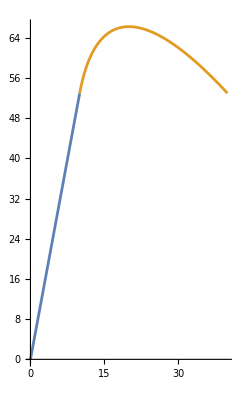

```mathematica
f[l_]:={{1. (1-l) l+l^2},{1. (1-l) l+2 l^2}};
f[l_] := Subscript[curva, 1]
f1[l_] := Subscript[curva, 2]
f2[l_] := Subscript[curva, 3]
f3[l_] := Subscript[curva, 4]
ParametricPlot[{f[l],f1[l]},{l,0,1}]
```

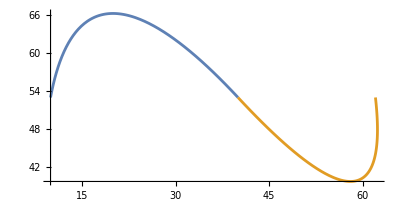

```mathematica
ParametricPlot[{f1[l],f2[l]},{l,0,1}]
```

```mathematica
Subscript[Q, 1]= Subscript[Q, 1]/.sol;
Subscript[P, 0] = Transpose[Subscript[P, 0]]
Subscript[P, 1] = Transpose[Subscript[P, 1]];
Subscript[P, 2] = Transpose[Subscript[P, 2]];
spline=BSplineCurve[{Subscript[P, 0],Subscript[P, 1],Subscript[P, 2],Subscript[Q, 0],Subscript[Q, 1],Subscript[Q, 2]},3]
Plot[spline,{l,0,1}]
```

{0}

{{0,0}}

BSplineCurve[{{{0,0}},{{5,53/2}},{{10,53}},{{10},{53}},{{{{{{{{{{{{15},{159/2}}}}}}}}}}}},{{40},{53}}},3]

-Graphics-

### Parametrico

```mathematica
Subscript[P, i_] := {{Subscript[a, i]},{Subscript[b, i]}}
```

```mathematica
Subscript[Q, i_] := {{Subscript[c, i]},{Subscript[d, i]}}
```

```mathematica
Subscript[P, 1]
```

{{5},{53/2}}

```mathematica
Subscript[P, 2]
```

{{10},{53}}

```mathematica
Subscript[B, 1]= Binomial[2,0]*Subscript[P, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[P, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[P, 2]*(1-l)^0*l^2
```

{{10 (1-l) l+10 l^2},{53 (1-l) l+53 l^2}}

```mathematica
Subscript[B, 2]= Binomial[2,0]*Subscript[Q, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[Q, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[Q, 2]*(1-l)^0*l^2
```

Thread::tdlen: Objects of unequal length in {{10 (1-l)^2},{53 (1-l)^2}}+{{{30 (1-l) l},{159 (1-l) l}}}+{{40 l^2},{53 l^2}} cannot be combined.

{{{30 (1-l) l},{159 (1-l) l}}}+{{10 (1-l)^2},{53 (1-l)^2}}+{{40 l^2},{53 l^2}}

```mathematica
Subscript[dB, 1] = D[Subscript[B, 1],l]
```

{{10 (1-l)+10 l},{53 (1-l)+53 l}}

```mathematica
Subscript[dB, 2] = D[Subscript[B, 2],l]
```

Thread::tdlen: Objects of unequal length in {{{30 (1+Times[«2»])-30 l},{159 (1+Times[«2»])-159 l}}}+{{-20 (1-l)},{-106 (1-l)}}+{{80 l},{106 l}} cannot be combined.

{{{30 (1-l)-30 l},{159 (1-l)-159 l}}}+{{-20 (1-l)},{-106 (1-l)}}+{{80 l},{106 l}}

```mathematica
eq = Flatten[(Subscript[dB, 1]/.l-> 1)] - Flatten[(Subscript[dB, 2]/.l-> 0) ]
```

Thread::tdlen: Objects of unequal length in {{{30},{159}}}+{{-20},{-106}}+{{0},{0}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{-30},{-159}}}+{{20},{106}}+{{0},{0}} cannot be combined.

Thread::tdlen: Objects of unequal length in {10,53}+{{{-30},{-159}}}+{{0},{0}}+{{20},{106}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{{-30},{-159}}}+{10,53}+{{0},{0}}+{{20},{106}}

```mathematica
sol = Solve[eq == 0]
```

{}

```mathematica
Subscript[curva, 1] = Subscript[B, 1]
```

{{10 (1-l) l+10 l^2},{53 (1-l) l+53 l^2}}

```mathematica
Subscript[curva, 2] = Subscript[B, 2]/.sol
```

{{{30 (1-l) l},{159 (1-l) l}}}+{{10 (1-l)^2},{53 (1-l)^2}}+{{40 l^2},{53 l^2}}

```mathematica
(Subscript[B, 1]) // MatrixForm
```

(10 (1-l) l+10 l^2
53 (1-l) l+53 l^2)

```mathematica
(Subscript[B, 2]) // MatrixForm
```

{{{30 (1-l) l},{159 (1-l) l}}}+{{10 (1-l)^2},{53 (1-l)^2}}+{{40 l^2},{53 l^2}}

```mathematica
Subscript[Q, 1]/.sol
```

{{{15},{159/2}}}

## Quattro punti

### Parametrico

```mathematica
Subscript[P, i_] := {{Subscript[a, i]},{Subscript[b, i]}}
```

```mathematica
Subscript[Q, i_] := {{Subscript[c, i]},{Subscript[d, i]}}
```

```mathematica
Subscript[P, 1]
```

{{5},{53/2}}

```mathematica
Subscript[P, 2]
```

{{10},{53}}

```mathematica
Subscript[B, 1]= Binomial[3,0]*Subscript[P, 0]*(1-l)^3*l^0+Binomial[3,1]*Subscript[P, 1]*(1-l)^2*l^1+Binomial[3,2]*Subscript[P, 2]*(1-l)^1*l^2+Binomial[3,3]*Subscript[P, 3]*(1-l)^0*l^3
```

{{15 (1-l)^2 l+30 (1-l) l^2+l^3 a_3},{159/2 (1-l)^2 l+159 (1-l) l^2+l^3 b_3}}

```mathematica
Subscript[B, 2]= Binomial[3,0]*Subscript[Q, 0]*(1-l)^3*l^0+Binomial[3,1]*Subscript[Q, 1]*(1-l)^2*l^1+Binomial[3,2]*Subscript[Q, 2]*(1-l)^1*l^2+Binomial[3,3]*Subscript[Q, 3]*(1-l)^0*l^3
```

Thread::tdlen: Objects of unequal length in {{10 (1-l)^3},{53 (1-l)^3}}+{{{45 (1+Times[«2»])^2 l},{477/2 (1+Times[«2»])^2 l}}}+{{120 (1-l) l^2},{159 (1-l) l^2}}+{{l^3 c_3},{l^3 d_3}} cannot be combined.

{{{45 (1-l)^2 l},{477/2 (1-l)^2 l}}}+{{10 (1-l)^3},{53 (1-l)^3}}+{{120 (1-l) l^2},{159 (1-l) l^2}}+{{l^3 c_3},{l^3 d_3}}

```mathematica
Subscript[dB, 1] = D[Subscript[B, 1],l]
```

{{15 (1-l)^2+30 (1-l) l-30 l^2+3 l^2 a_3},{159/2 (1-l)^2+159 (1-l) l-159 l^2+3 l^2 b_3}}

```mathematica
Subscript[dB, 2] = D[Subscript[B, 2],l]
```

Thread::tdlen: Objects of unequal length in {{{45 Plus[«2»]^2-90 (1+Times[«2»]) l},{477/2 Plus[«2»]^2-477 (1+Times[«2»]) l}}}+{{-30 (1-l)^2},{-159 (1-l)^2}}+{{240 (1-l) l-120 l^2},{318 (1-l) l-159 l^2}}+{{3 l^2 c_3},{3 l^2 d_3}} cannot be combined.

{{{45 (1-l)^2-90 (1-l) l},{477/2 (1-l)^2-477 (1-l) l}}}+{{-30 (1-l)^2},{-159 (1-l)^2}}+{{240 (1-l) l-120 l^2},{318 (1-l) l-159 l^2}}+{{3 l^2 c_3},{3 l^2 d_3}}

```mathematica
eq = Flatten[(Subscript[dB, 1]/.l-> 1)] - Flatten[(Subscript[dB, 2]/.l-> 0) ]
```

Thread::tdlen: Objects of unequal length in {{{45},{477/2}}}+{{-30},{-159}}+{{0},{0}}+{{0},{0}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{45},{477/2}}}+{{-30},{-159}}+{{0},{0}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{-45},{-477/2}}}+{{30},{159}}+{{0},{0}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{{-45},{-477/2}}}+{{0},{0}}+{{30},{159}}+{-30+3 a_3,-159+3 b_3}

```mathematica
sol = Solve[eq == 0]
```

Thread::tdlen: Objects of unequal length in {{{-45},{-477/2}}}+{{0},{0}}+3 Reduce`ReduceVar[2] cannot be combined.

Thread::tdlen: Objects of unequal length in {{{-45},{-477/2}}}+{{0},{0}}+3 Reduce`ReduceVar[1] cannot be combined.

Thread::tdlen: Objects of unequal length in {{{-45},{-477/2}}}+{{0},{0}}+3 Reduce`ReduceVar[2] cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{a_3→1/3 ({{{45},{477/2}}}+{{0},{0}}),b_3→1/3 ({{{45},{477/2}}}+{{0},{0}})}}

```mathematica
Subscript[curva, 1] = Subscript[B, 1]
```

{{15 (1-l)^2 l+30 (1-l) l^2+l^3 a_3},{159/2 (1-l)^2 l+159 (1-l) l^2+l^3 b_3}}

```mathematica
Subscript[curva, 2] = Subscript[B, 2]/.sol
```

{{{{45 (1-l)^2 l},{477/2 (1-l)^2 l}}}+{{10 (1-l)^3},{53 (1-l)^3}}+{{120 (1-l) l^2},{159 (1-l) l^2}}+{{l^3 c_3},{l^3 d_3}}}

```mathematica
(Subscript[B, 1]) // MatrixForm
```

(15 (1-l)^2 l+30 (1-l) l^2+l^3 a_3
159/2 (1-l)^2 l+159 (1-l) l^2+l^3 b_3)

```mathematica
(Subscript[B, 2]) // MatrixForm
```

{{{45 (1-l)^2 l},{477/2 (1-l)^2 l}}}+{{10 (1-l)^3},{53 (1-l)^3}}+{{120 (1-l) l^2},{159 (1-l) l^2}}+{{l^3 c_3},{l^3 d_3}}

```mathematica
Subscript[Q, 1]/.sol
```

{{{{15},{159/2}}}}